# Evolutionary dynamics under accelerating returns

```mathematica
Clear["Global`*"]; 
SetDirectory[NotebookDirectory[]];
```

## 1. Functions

```mathematica
blue=RGBColor["#0A71B7"]
orange= RGBColor["#D25F02"]
```

RGBColor[0.0392156862745098, 0.44313725490196076, 0.7176470588235294]

RGBColor[0.8235294117647058, 0.37254901960784315, 0.00784313725490196]

```mathematica
Functions = { Bc->Function[k,n(k/n)^u β]};
```

```mathematica
values={n->4,β->1,Cc-> 0.3,δ->1.,u->2.,cd->0.75} ;

cm=72/2.54;
```

## 2. Evolutionary dynamics (Fig 6b-c)

### 2.1 Invasion and fixation of cooperation

This numerical analyses iterates a perturbation in the direction of the selection gradient vector on the population traits' values. We start from a population of  defectors expressing initial phenotypic value z0={d^*, 0.4,0.6,0.7,0.9,0}. It stops the iteration once the population expresses  z = 1 . This corresponds to the procedure described in Appendix D.1.

```mathematica
ntest = n /. values;
cdtest = cd  /. values;
utest = u /. values;
valuesNeutral={n->ntest,β->0,Cc-> 0,cd->cdtest,u-> utest} ;
m[k_]:=fecdisp[d[n+1]] /(fecpatch[k](1-d[k])+fecdisp[d[n+1]] )/.δ->0;
d0baseline=2/(1+2 cd n+√(1+4 cd^2 (-1+n) n))/.Functions//.values;
solR2=Flatten[Solve[(R2 == ∑_(c0=0)^n (1-m[c0])^2(1/n+(n-1)/n R2)Pk0[c0,d[n+1],n]/.valuesNeutral/.Functions//.valuesNeutral),R2]];
Pk0[k_,z_,n_]:=z^k(1-z)^(n-k)Binomial[n,k];(* Probability that there is k cooperators among n individuals when the population is monomorphic for z *)
fec[k_,j_]:=(1+δ (Bc[k]/n-Cc j)) (* fecundity of an individual either cooperating (j=1) or defecting (j=0) in a group with k cooperators *)
fecpatch[k_]:=(1+ δ((k /n)(Bc[k]/n-Cc )+(1-k/n)(Bc[k]/n)));
(* average fecundity in a patch with k cooperators*)
fecphilo[k_]:=fecpatch[k](1-d[k]);(* offspring produced that will remain in their local patch *)
fecdisp[z_]:= ∑_(k2=0)^n d[k2] (1-cd) fecpatch[k2]Pk0[k2,z,n];
(* number of offspring coming into an arbirary patch when the population is monomorphic for z *)

w=∑_(c0=0)^(n-3) ∑_(c3=0)^1 ∑_(c2=0)^1 ∑_(c1=0)^1 fec[c1+c2+c3+c0,c1]((  1-d[1,c1+c2+c3+c0])/(( (1-d[1,c1+c2+c3+c0]) fec[c1+c2+c3+c0,c1]/n+ (1-d[2,c1+c2+c3+c0]) fec[c1+c2+c3+c0,c2]/n+(1-d[3,c1+c2+c3+c0])fec[c1+c2+c3+c0,c3]/n+(1-d[c1+c2+c3+c0]) ((n-3-c0)fec[c1+c2+c3+c0,0]/n+c0 fec[c1+c2+c3+c0,1]/n) )+ fecdisp[d[n+1]]) + ∑_(k0=0)^n ((d[1,c1+c2+c3+c0](1-cd) )/( fecphilo[k0]+ fecdisp[d[n+1]]))Pk0[k0,d[n+1],n])d[1,n+1]^c1(1-d[1,n+1])^(1-c1) d[2,n+1]^c2(1-d[2,n+1])^(1-c2)d[3,n+1]^c3(1-d[3,n+1])^(1-c3) Pk0[c0,d[n+1],n-3]/.values/.Functions//.values;
monopop=Flatten[Table[{ d[i,k]-> d[k]},{k,0,ntest+1},{i,1,3}]];
S=
Table[
D[w, d[1,k]]+ (n-1)R2 D[w, d[2,k]]/. solR2 /. monopop /.Functions//.values
,{k,0,ntest+1}];
```

```mathematica
Δz[u_]:=Clip[ u+G.(S/. Table[d[k]-> u[[1+k]],{k,0,ntest+1}] ),{0.,1.}];
```

```mathematica
z0 = {d0baseline,0.4,0.6,0.7,0.9,0};
G =0.1 IdentityMatrix[ntest+2];
res = NestWhileList[Δz,z0,EuclideanDistance[#1,#2]>10^-5&,2,5000];
```

```mathematica
p1=ListLinePlot[Flatten[res,{2}][[1;;ntest+1]],PlotRange->{0,1}, PlotStyle->Map[Lighter[blue,#]&,Reverse[Range[0,0.8,N[0.8/(ntest)]]]]];
```

```mathematica
p2=ListLinePlot[Flatten[res,{2}][[ntest+2]],PlotRange->{0,1},PlotStyle->Directive[orange]];
```

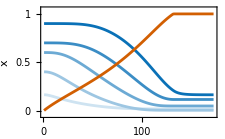

```mathematica
Show[p1,p2,Frame->True,FrameTicks->{{{0,.5,1},None},{{0,50,100,150},None}},ImageSize->8 cm,FrameLabel->{"generation",x̄},LabelStyle->Directive[FontFamily->"Arial",FontSize->10,Black],PlotRange->{-0.05,1.05},RotateLabel->False]
```

```mathematica
Export["Accelerating_Invade.pdf",Show[%,ImageSize->6.5cm]]
```

Accelerating_Invade.pdf

### 2.1 Loss cooperation

We follow the same procedure as in the previous section but starting from z0={0.9,0.7,0.55,0.4,d^*,1}. It stops the iteration once the population expresses  z = 1 . This corresponds to the procedure described in Appendix D.1.

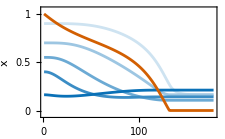

```mathematica
z0 =  {0.9,0.7,0.55,0.4,d0baseline,1.};
G =0.1 IdentityMatrix[ntest+2];
res = NestWhileList[Δz,z0,EuclideanDistance[#1,#2]>10^-5&,2,5000];
p1=ListLinePlot[Flatten[res,{2}][[1;;ntest+1]],PlotRange->{0,1}, PlotStyle->Map[Lighter[blue,#]&,Reverse[Range[0,0.8,N[0.8/(ntest)]]]]];
p2=ListLinePlot[Flatten[res,{2}][[ntest+2]],PlotRange->{0,1},PlotStyle->Directive[orange]];
Show[p1,p2,Frame->True,FrameTicks->{{{0,.5,1},None},{{0,50,100,150},None}},ImageSize->8 cm,FrameLabel->{"generation",x̄},LabelStyle->Directive[FontFamily->"Arial",FontSize->10,Black],PlotRange->{-0.05,1.05},RotateLabel->False]
```

```mathematica
Export["Accelerating_Loss.pdf",Show[%,ImageSize->6.5cm]]
```

Accelerating_Loss.pdf

## 3.Basin of attraction (Fig 6a)

This numerical analyses repeat the  procedure presented above for 5’000 randomly dispersal strategies (in an initial population of full defectors). It keeps track of the proportion of the initial strategies that lead to the fixation of cooperation from rarity. This corresponds to the procedure described in Appendix D.2.

```mathematica
NumericAnalysesInvade=Table[
Print[cdi];

values={n->4,β->4,Cc-> 0.3,δ->1.,u->2.,cd-> cdi} ;
ntest = n /. values;
cdtest = cd  /. values;
utest = u /. values;
valuesNeutral={n->ntest,β->0,Cc-> 0,cd->cdtest,u-> utest} ;
m[k_]:=fecdisp[d[n+1]] /(fecpatch[k](1-d[k])+fecdisp[d[n+1]] )/.δ->0;
d0baseline=2/(1+2 cd n+√(1+4 cd^2 (-1+n) n))/.values;
solR2=Flatten[Solve[(R2 == ∑_(c0=0)^n (1-m[c0])^2(1/n+((n-1)/n)R2)Pk0[c0,d[n+1],n]/.valuesNeutral/.Functions//.valuesNeutral),R2]];
Pk0[k_,z_,n_]:=z^k(1-z)^(n-k)Binomial[n,k];(* Probability that there is k cooperators among n individuals when the population is monomorphic for z *)
fec[k_,j_]:=(1+δ (Bc[k]/n-Cc j)) ;(* fecundity of an individual either cooperating (j=1) or defecting (j=0) in a group with k cooperators *)
fecpatch[k_]:=(1+ δ((k /n)(Bc[k]/n-Cc )+(1-k/n)(Bc[k]/n)));
(* average fecundity in a patch with k cooperators*)
fecphilo[k_]:=fecpatch[k](1-d[k]);(* offspring produced that will remain in their local patch *)
fecdisp[z_]:= ∑_(k2=0)^n d[k2] (1-cd) fecpatch[k2]Pk0[k2,z,n];
w=∑_(c0=0)^(n-3) ∑_(c3=0)^1 ∑_(c2=0)^1 ∑_(c1=0)^1 fec[c1+c2+c3+c0,c1]((  1-d[1,c1+c2+c3+c0])/(( (1-d[1,c1+c2+c3+c0]) fec[c1+c2+c3+c0,c1]/n+ (1-d[2,c1+c2+c3+c0]) fec[c1+c2+c3+c0,c2]/n+(1-d[3,c1+c2+c3+c0])fec[c1+c2+c3+c0,c3]/n+(1-d[c1+c2+c3+c0]) ((n-3-c0)fec[c1+c2+c3+c0,0]/n+c0 fec[c1+c2+c3+c0,1]/n) )+ fecdisp[d[n+1]]) + ∑_(k0=0)^n ((d[1,c1+c2+c3+c0](1-cd) )/( fecphilo[k0]+ fecdisp[d[n+1]]))Pk0[k0,d[n+1],n])d[1,n+1]^c1(1-d[1,n+1])^(1-c1) d[2,n+1]^c2(1-d[2,n+1])^(1-c2)d[3,n+1]^c3(1-d[3,n+1])^(1-c3) Pk0[c0,d[n+1],n-3]/.values/.Functions//.values;
monopop=Flatten[Table[{ d[i,k]-> d[k]},{k,0,ntest+1},{i,1,3}]];
S=
Table[
D[w, d[1,k]]+ (n-1)R2 D[w, d[2,k]]/. solR2 /. monopop /.values
,{k,0,ntest+1}];
res=
ParallelTable[
z0Random=Append[ Table[ RandomReal[{10^-5,1-10^-5}],{k,1,ntest+1}] ,0.];
z0= z0Random;
z0[[1]]= d0baseline;
G =0.1 IdentityMatrix[ntest+2];
Δz[u_]:=Clip[ u+G.(S/. Table[d[k]-> u[[1+k]],{k,0,ntest+1}] ),{0.,1.}];
ngenmax=5000;
res0=NestWhile[Δz,z0,Abs[#1[[ntest+2]]-#2[[ntest+2]]]>10^-8&,2,ngenmax];
fix0=Last[res0];
fix0
,
{i,5000}
];
Print[Mean[res]];
{cdi,Mean[res]} 
,{cdi,0.05,0.95,0.1}
]
```

0.05

0.

0.15

0.

0.25

0.

0.35

7.72226×10^-8

0.45

0.

0.55

0.2

0.65

0.4

0.75

0.6

0.85

0.7

0.95

0.6

{{0.05,0.},{0.15,0.},{0.25,0.},{0.35,7.72226×10^-8},{0.45,0.},{0.55,0.2},{0.65,0.4},{0.75,0.6},{0.85,0.7},{0.95,0.6}}

```mathematica
NumericAnalysesInvade={{0.05,0.},{0.15000000000000002,0.},{0.25,0.},{0.35000000000000003,0.},{0.45,1.2789575047967988*^-6},{0.55,0.12160038066118917},{0.6500000000000001,0.3144004297185935},{0.7500000000000001,0.4462010579604418},{0.8500000000000001,0.541401318890271},{0.9500000000000001,0.5874042299290491}} ;
```

Here we repeat the  procedure but starting with an initial population of full cooperators. We keeps track of the proportion of the initial strategies that lead to the loss of cooperation from fixation .

```mathematica
NumericAnalysesLoss=Table[
Print[cdi];

values={n->4,β->4,Cc-> 0.3,δ->1.,u->2.,cd-> cdi} ;
ntest = n /. values;
cdtest = cd  /. values;
utest = u /. values;
valuesNeutral={n->ntest,β->0,Cc-> 0,cd->cdtest,u-> utest} ;
d0baseline=2/(1+2 cd n+√(1+4 cd^2 (-1+n) n))/.values;
Pk0[k_,z_,n_]:=z^k(1-z)^(n-k)Binomial[n,k];(* Probability that there is k cooperators among n individuals when the population is monomorphic for z *)
fec[k_,j_]:=(1+δ (Bc[k]/n-Cc j)) ;(* fecundity of an individual either cooperating (j=1) or defecting (j=0) in a group with k cooperators *)
fecpatch[k_]:=(1+ δ((k /n)(Bc[k]/n-Cc )+(1-k/n)(Bc[k]/n)));
(* average fecundity in a patch with k cooperators*)
fecphilo[k_]:=fecpatch[k](1-d[k]);(* offspring produced that will remain in their local patch *)
fecdisp[z_]:= ∑_(k2=0)^n d[k2] (1-cd) fecpatch[k2]Pk0[k2,z,n];
m[k_]:=fecdisp[d[n+1]] /(fecpatch[k](1-d[k])+fecdisp[d[n+1]] )/.δ->0;
solR2=Flatten[Solve[(R2 == ∑_(c0=0)^n (1-m[c0])^2(1/n+((n-1)/n)R2)Pk0[c0,d[n+1],n]/.valuesNeutral/.Functions//.valuesNeutral),R2]];
w=∑_(c0=0)^(n-3) ∑_(c3=0)^1 ∑_(c2=0)^1 ∑_(c1=0)^1 fec[c1+c2+c3+c0,c1]((  1-d[1,c1+c2+c3+c0])/(( (1-d[1,c1+c2+c3+c0]) fec[c1+c2+c3+c0,c1]/n+ (1-d[2,c1+c2+c3+c0]) fec[c1+c2+c3+c0,c2]/n+(1-d[3,c1+c2+c3+c0])fec[c1+c2+c3+c0,c3]/n+(1-d[c1+c2+c3+c0]) ((n-3-c0)fec[c1+c2+c3+c0,0]/n+c0 fec[c1+c2+c3+c0,1]/n) )+ fecdisp[d[n+1]]) + ∑_(k0=0)^n ((d[1,c1+c2+c3+c0](1-cd) )/( fecphilo[k0]+ fecdisp[d[n+1]]))Pk0[k0,d[n+1],n])d[1,n+1]^c1(1-d[1,n+1])^(1-c1) d[2,n+1]^c2(1-d[2,n+1])^(1-c2)d[3,n+1]^c3(1-d[3,n+1])^(1-c3) Pk0[c0,d[n+1],n-3]/.values/.Functions//.values;
monopop=Flatten[Table[{ d[i,k]-> d[k]},{k,0,ntest+1},{i,1,3}]];
S=
Table[
D[w, d[1,k]]+ (n-1)R2 D[w, d[2,k]]/. solR2 /. monopop /.values
,{k,0,ntest+1}];
res=
ParallelTable[
z0Random=Append[ Table[ RandomReal[{10^-5,1-10^-5}],{k,1,ntest+1}] ,1.];
z0= z0Random;
z0[[ntest+1]]= d0baseline;
G =0.1 IdentityMatrix[ntest+2];
Δz[u_]:=Clip[ u+G.(S/. Table[d[k]-> u[[1+k]],{k,0,ntest+1}] ),{0.,1.}];
ngenmax=5000;
res0=NestWhile[Δz,z0,Abs[#1[[ntest+2]]-#2[[ntest+2]]]>10^-8&,2,ngenmax];
fix0=Last[res0];
1-fix0
,
{i,10}
];
Print[Mean[res]];
{cdi,Mean[res]} 
,{cdi,0.05,0.95,0.1}
]
```

0.05

0.

0.15

0.

0.25

5.04685×10^-8

0.35

0.

0.45

3.31094×10^-8

0.55

0.

0.65

0.

0.75

0.3

0.85

0.1

0.95

0.4

{{0.05,0.},{0.15,0.},{0.25,5.04685×10^-8},{0.35,0.},{0.45,3.31094×10^-8},{0.55,0.},{0.65,0.},{0.75,0.3},{0.85,0.1},{0.95,0.4}}

```mathematica
NumericAnalysesLoss={{0.05,0.},{0.15000000000000002,0.},{0.25,0.},{0.35000000000000003,4.193884136107462*^-6},{0.45,5.376105665069297*^-6},{0.55,3.837735863800096*^-6},{0.6500000000000001,0.05080407347913721},{0.7500000000000001,0.16860490777832537},{0.8500000000000001,0.2590091647335485},{0.9500000000000001,0.35462026642560085}}
```

{{0.05,0.},{0.15,0.},{0.25,0.},{0.35,4.19388×10^-6},{0.45,5.37611×10^-6},{0.55,3.83774×10^-6},{0.65,0.0508041},{0.75,0.168605},{0.85,0.259009},{0.95,0.35462}}

```mathematica
plot = PairedBarChart[Reverse[NumericAnalysesLoss[[All,2]]],Reverse[ NumericAnalysesInvade[[All,2]]],BarSpacing->{0.3,Automatic,.3},ChartLabels->Reverse[Table[cdi,{cdi,0.05,0.95,0.1}]],ChartStyle->{{Directive[White,EdgeForm[Directive[orange,Thickness[0.0027]]]],Directive[orange,EdgeForm[orange]]},None,None},LabelStyle->Directive[FontFamily->"Arial",FontSize->11,Black],ImageSize->10cm,PlotRange-> {0,1},PlotRangePadding->0.,PlotLabel->Subscript[c, d]]
```

-Graphics-

```mathematica
Export["file6.pdf",plot,ImageSize->10cm]
```

file6.pdf